```mathematica
ClearAll["Global`*"]
$Assumptions[Element[t,Reals],Element[ϵ,Reals],Element[s,Reals]]
$Assumptions[Element[x[t],Reals],Element[y[t],Real],Element[w[t],Real]]
system={x''[t]==-y'[t]w[t],y''[t]==x'[t]w[t],w'[t]==ϵ}
initialv={x'[0]==0,y'[0]==s}
initial={x[0]==0,y[0]==0,w[0]==0}
```

True[t∈ℝ,ϵ∈ℝ,s∈ℝ]

Element::bset: The second argument Real of Element should be one of: Primes, Integers, Rationals, Algebraics, Reals, Complexes, or Booleans.

True[x[t]∈ℝ,y[t]∈Real,w[t]∈Real]

{x''[t]==-w[t] y'[t],y''[t]==w[t] x'[t],w'[t]==ϵ}

{x'[0]==0,y'[0]==s}

{x[0]==0,y[0]==0,w[0]==0}

```mathematica
equations = Join[system, initialv, initial]
res = DSolve[equations, {x,y,w},{t, 0, 10}]
```

{x''[t]==-w[t] y'[t],y''[t]==w[t] x'[t],w'[t]==ϵ,x'[0]==0,y'[0]==s,x[0]==0,y[0]==0,w[0]==0}

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1/(√π √ϵ) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2 ArcCos[Cos[1^2/(2 ϵ)]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{x→Function[{t},-(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)],y→Function[{t},(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)],w→Function[{t},t ϵ]}}

```mathematica
sx[t_]=D[x[t]/.res[[1]],t]
sy[t_]=D[y[t]/.res[[1]],t]
```

-s Sin[(t^2 ϵ)/2]

s Cos[(t^2 ϵ)/2]

```mathematica
xr[t_]:=Evaluate[x[t]/.res[[1]]]
yr[t_]:=Evaluate[y[t]/.res[[1]]]
$Assumptions[Element[xr[t],Real],Element[yr[t],Real],Element[sx[t],Real],Element[sy[t],Real]]
```

Element::bset: The second argument Real of Element should be one of: Primes, Integers, Rationals, Algebraics, Reals, Complexes, or Booleans.

General::stop: Further output of Element::bset will be suppressed during this calculation.

True[-(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)∈Real,(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)∈Real,-s Sin[(t^2 ϵ)/2]∈Real,s Cos[(t^2 ϵ)/2]∈Real]

```mathematica
tangentLine=(Y-yr[t])==(sy[t]/sx[t]) (X-xr[t]);
tres=Solve[tangentLine, t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[Y-(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)==-Cot[(t^2 ϵ)/2] (X+(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)),t]

```mathematica
X=2
Y =8
ϵ=-0.1
s=2.0
tres=Solve[tangentLine, t]
```

2

8

-0.1

2.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[8+(0.+11.21 ⅈ) FresnelC[(0.+0.178412 ⅈ) t]==Cot[0.05 t^2] (2-(0.+11.21 ⅈ) FresnelS[(0.+0.178412 ⅈ) t]),t]

```mathematica
t1=t/.tres[[1]]
```

3.11461

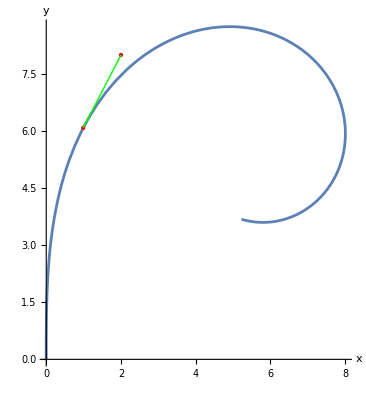

```mathematica
ParametricPlot[{xr[t],yr[t]},{t,0,10},AspectRatio->Automatic,AxesLabel->{"x","y"},
Epilog -> {
Red,PointSize[Large], Point[{xr[t1],yr[t1]}],
Red,PointSize[Large], Point[{X,Y}],
Green, Thick, Line[{{xr[t1],yr[t1]},{X,Y}}]
}]
```